```mathematica
e = 0.0015;
d = 0.005;
nu = 1.79 * 10^-5;
q = 1.23;
V = 40;
re = q * V * d / nu;
f := 1.325 / (Log[(e/(3.7 * d) +  5.74/(re)^0.9)]) ^ 2;
g[y_]:= 1/Sqrt[y] + 2.0* Log10[e/(3.7d)+2.51/(re*Sqrt[y])];
```

```mathematica
NewtonRaphson[f_, x0_, max_] := Module[{},
k=0;
p0=N[x0];
p1=p0;
While[k<max,
p0=p1;
p1=p0 - N[f[p0]]/N[f'[p1]];
k++;
];
Return[p1];
];
SecantMethod[f_, x0_, x1_, max_] := Module[{},
k=1;
p0=N[x0];
p1=N[x1];
p2=p1;
p1=p0;
While[k<max,
p0=p1;
p1=p2;
p2=p1 - (f[p1]*(p1-p0)) / (f[p1]-f[p0]);
k++;
];
Return[p2];
];
```

```mathematica
SecantMethod[g, 0.08, 0.008, 10]
```

0.210824

```mathematica
g[f]
```

-0.00689922

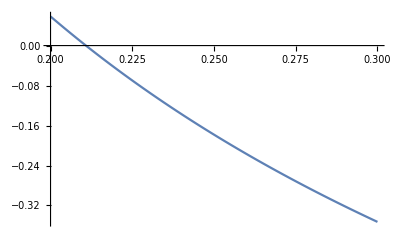

0.008

```mathematica
Plot[g[y], {y, 0.2, 0.3}]
```

```mathematica
NSolve[g[y]==0]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{y->0.21082400427756523}}
Roots[g[y]==0, y]
```

{{y→0.210824}}

Roots::neq: 1.+0.868589 √y Log[0.0810811+0.000182638/(√y)] is expected to be a polynomial in the variable y.

Roots[1/(√y)+0.868589 Log[0.0810811+0.000182638/(√y)]==0,y]

```mathematica
Roots[g[y]]
```

Roots::argr: Roots called with 1 argument; 2 arguments are expected.

Roots[1/(√y)+0.868589 Log[0.0810811+0.000182638/(√y)]]